## MODELAGEM DA DINÂMICA PLANA DE AERONAVE SUPERSÔNICA DE PASSAGEIROS DURANTE FASE DE FREE-ROLL DA ATERRISSAGEM

## PME3380 - Modelagem de Sistemas Dinâmicos Prof. Dr. Agenor de Toledo Fleury Prof. Dr. Renato Maia Matarazzo Orsino

## Grupo K Lucas Retore Carboni - 12676091 Roberto Tetsuo Hamaoka - 10334770 Vitor Lucas Buter - 12555700

## Modelo principal - toque e free-roll

O equacionamento é baseado no seguinte modelo físico:
-Graphics-

Importando as funções necessárias ao código

```mathematica
SetDirectory @ NotebookDirectory[];
<<Linearize.m
```

As coordenadas generalizadas são definidas como:

```mathematica
𝕢[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t]};
𝕧[t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]}; 
𝕦[t_] = {Fa[t], Ta[t]}; (*Será positiva no sentido positivo do eixo y; Será positivo no sentido antihorário*)
[t_]= {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = { Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, 𝕧[t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
α = 𝕢[t][[3]] + Subscript[Φ, 0];
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, PO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor P-O*)
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, GO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor G-O*)
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

```mathematica
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
D[Subscript[H, o], t] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
-Subscript[M, peso] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- 𝕦[t][[2]] - Subscript[M, aero] -Subscript[M, peso]) [[3]];
```

### Aplicação do TMB no conjunto do trem de pouso (m) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]] //FullSimplify;
Subscript[TMB, m] = m*(D[𝕧[t][[1]], t]) + Subscript[k, r]*(𝕢[t][[1]] - [t][[1]]) + Subscript[c, r]*(D[(𝕢[t][[1]] - [t][[1]]), t]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + 𝕦[t][[1]]//FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) - 𝕦[t][[1]] - Subscript[L, ext][[2]]//FullSimplify;
```

### O espaço de estados

```mathematica
DIN = {Subscript[TMB, m], Subscript[TMB, M], TQMA};

Sol[t_] = Flatten @ Solve[
	(# == 0)& /@ DIN,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;

𝕩[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
F = (𝕩'[t] /.Sol[t]); 
F //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(-Fa[t]+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])-(c_r+c_t) q_1'[t]+c_t q_2'[t]+c_r y_ext'[t])/m
(M D_GO^2 (-4 g M Cos[Φ_0+θ[t]]^2+Sin[2 (Φ_0+θ[t])] (2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol)+M D_GO (S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2+4 Cos[Φ_0+θ[t]] Ta[t]-4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2)-2 J_oz (2 Fa[t]+S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(4 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
-(Sec[Φ_0+θ[t]] (2 Sec[Φ_0+θ[t]] Ta[t]+S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D Tan[Φ_0+θ[t]])-2 M Sin[Φ_0+θ[t]] D_GO^2 θ'[t]^2+D_GO (-2 Fa[t]-S ρ C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])+2 (-g M+g M μ_rol Tan[Φ_0+θ[t]]+k_t (-q_1[t]+q_2[t])+c_t (-q_1'[t]+q_2'[t])))))/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz))

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
POSequi = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINlin = Linearize[DIN, POSequi]; (*ELS -> Equação dinâmica não-linear*)

Sollin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINlin,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
	
Subscript[𝕩, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[F, lin] = (Subscript[𝕩, lin]'[t] /.Sollin[t]);
Subscript[F, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(-Fa[t]+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])-(c_r+c_t) q_1'[t]+c_t q_2'[t]+c_r y_ext'[t])/m
(2 M Cos[Φ_0] D_GO^2 ((2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])+2 g M (-Cos[Φ_0]+Sin[Φ_0] θ[t]))+2 M Cos[Φ_0] D_GO (2 Ta[t]+S ρ D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t])))-2 J_oz (2 Fa[t]+S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(4 M (M Cos[Φ_0]^2 D_GO^2-J_oz))
(Sec[Φ_0] (-2 Sec[Φ_0] Ta[t]+S ρ D_PO (u_longit+u_vento)^2 (-C_D (Tan[Φ_0]+θ[t])+C_L (-1+Tan[Φ_0] θ[t]))+D_GO (2 Fa[t]+S ρ C_L (u_longit+u_vento)^2 (1+μ_rol (Tan[Φ_0]+θ[t]))-2 (-g M+g M Tan[Φ_0] θ[t]+g M μ_rol (Tan[Φ_0]+θ[t])+k_t (-q_1[t]+q_2[t])+c_t (-q_1'[t]+q_2'[t])))))/(2 M D_GO^2-2 Sec[Φ_0]^2 J_oz))

```mathematica
rep = {Subscript[C, D] -> (0.0139*(180*(Subscript[Φ, 0])/Pi) - 0.0248), Subscript[C, L] -> (0.04264*(180*Subscript[Φ, 0]/Pi) - 0.0158),  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 1360000, Subscript[c, r] -> 9700, m -> 4000, M -> 88000, S -> 88000/285, Subscript[D, GO] -> 3.5, Subscript[D, PO] -> 5, ρ -> 1.2923, Subscript[J, oz] -> 16864415,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
(*CD e CL deveriam, na verdade, estar multiplicando o ângulo de ataque α anteriormente definido. Contudo, como a linearização é feita em torno de θ = 0, α = Subscript[Φ, 0] para o modelo linear*)

𝔸 = CoefficientArrays[Subscript[F, lin], Subscript[𝕩, lin][t]][[2]]//Normal; 
𝔸  //MatrixForm;

𝔹 = CoefficientArrays[Subscript[F, lin], 𝕦[t]][[2]]//Normal; 
𝔹 //MatrixForm;

𝔼 = CoefficientArrays[Subscript[F, lin], [t]][[2]]//Normal; 
𝔼 //MatrixForm;

𝔹U𝔼 = MapThread[Append, {𝔼, 𝔹}];
𝔹U𝔼 = Flatten /@ 𝔹U𝔼;
𝔹U𝔼 //MatrixForm;

uw = {{[t][[1]]}, {[t][[2]]}, {𝕦[t][[1]]}, {𝕦[t][[2]]}};
uw //MatrixForm;

ℂ = { {0,1,0,0,0,0}, {0,0,1,0,0,0}, {0,0,0,0,1,0}, {0,0,0,0,0,1}};
ℂ //MatrixForm;

𝔻 = {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
𝔻c = {{0,0},{0,0},{0,0},{0,0}};
𝔻 //MatrixForm;
```

### Substituindo os valores numéricos

```mathematica
SS = StateSpaceModel[{𝔸/.(rep)/.(Subscript[Φ, 0]->18*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹U𝔼/.(rep)/.(Subscript[Φ, 0]->13*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂ, 𝔻}]
```

000100000000001000000000010000-32117/1028717/100-13987/50025549/1000034097/40-1/40000138.542-138.542-0.1686511.23258-1.232580000.0000120978-2.15283×10^-7-2.40642.40640.0506657-0.02140930.0214093000-2.15283×10^-76.31275×10^-80100000000001000000000001000000000010000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic4461FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TF = TransferFunctionModel[SS, s]
```

```mathematica
(419.0782865142377 (-5.365549861524551-0.04773633506706509 s+112.39970253238874 s^2+s^3))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(2.9890142494031124 (-5.365549861524409-0.04773633506706521 s+112.39970253238756 s^2+s^3))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(0.00001209781612487859 (-16.417206776627886-0.11746608567562038 s+348.6978841296814 s^2+2.5028075099031595 s^3+s^4))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(8.381898624065798*^-7+7.300712923097307*^-9 s-0.000691425047989469 s^2-6.022335696798109*^-6 s^3-2.1528330762521364*^-7 s^4)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)-(7.279154222068654 (-1.9991217089821954*^-12-3.6116944937666606*^-14 s+112.3997025323895 s^2+s^3))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)-(0.05191749702510151 (-8.759038415634696*^-12+1.3685997524429212*^-13 s+112.39970253213025 s^2+s^3))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(-0.00024263593104478784-3.889253427757921*^-6 s-0.0000905552733456716 s^2-6.763654027963639*^-7 s^3-2.1528330762521364*^-7 s^4)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(0.0027974341955996347+0.000044840558508951744 s+0.00021115178242325783 s^2+1.8391280036667015*^-6 s^3+6.312711775535718*^-8 s^4)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(419.0782865142378 (-5.3655498615245465 s-0.047736335067047546 s^2+112.39970253238866 s^3+s^4))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(2.989014249403226 (-5.365549861524178 s-0.04773633506637877 s^2+112.39970253238083 s^3+s^4))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(0.000012097815975664616 (-1.1276763139757092*^-7-16.41720663259152 s-0.11746297485528205 s^2+348.6978810348299 s^3+2.502807550169989 s^4+s^5))/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(-1.3642420526593924*^-12+8.381926832612407*^-7 s+7.341441232711076*^-9 s^2-0.0006914251150647033 s^3-6.0223346736165695*^-6 s^4-2.1528330051978628*^-7 s^5)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(-818.1747692479067 s^3-7.2791542220688825 s^4)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(-5.835511221841671 s^3-0.05191749702453308 s^4)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(-1.3642420526593924*^-12-0.0002426359299434466 s-3.889217623509467*^-6 s^2-0.00009055531268131743 s^3-6.763643796148244*^-7 s^4-2.1528330051978628*^-7 s^5)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)(-1.3642420526593924*^-12+0.0027974341971486183 s+0.00004484059172682464 s^2+0.00021115174558872238 s^3+1.8391287994745653*^-6 s^4+6.31274659212977*^-8 s^5)/(-2248.585442174411-36.04296649635438 s+46934.795526017224 s^2+753.5664375757874 s^3+3353.1803330796365 s^4+29.20658319563011 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s44419.07828651423772.98901424940311240.000012097816124878598.381898624065798e-7-7.279154222068654-0.05191749702510151-0.000242635931044787840.0027974341955996347419.07828651423782.9890142494032260.000012097815975664616-1.3642420526593924e-12-818.1747692479067-5.835511221841671-1.3642420526593924e-12-1.3642420526593924e-12-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.585442174411-2248.5854421744111FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
TransferFunctionPoles[TF][[2]][[1]] //MatrixForm;
```

```mathematica
TransferFunctionZeros[TF] //MatrixForm ;
```

```mathematica
den = TF[[1]][[2]][[1]][[1]];
(*TF[[TOTAL]][[[NUMERADORES]]][[[LINHA]]][[COLUNA]]*) 

fq2y = TF[[1]][[1]][[1]][[1]]/den;
ftty = TF[[1]][[1]][[2]][[1]]/den;
fDq2y = TF[[1]][[1]][[3]][[1]]/den;
fDtty = TF[[1]][[1]][[4]][[1]]/den;

fq2Dy = TF[[1]][[1]][[1]][[2]]/den;
fttDy = TF[[1]][[1]][[2]][[2]]/den;
fDq2Dy = TF[[1]][[1]][[3]][[2]]/den;
fDttDy = TF[[1]][[1]][[4]][[2]]/den;

fq2F = TF[[1]][[1]][[1]][[3]]/den;
fttF = TF[[1]][[1]][[2]][[3]]/den
fDq2F = TF[[1]][[1]][[3]][[3]]/den;
fDttF = TF[[1]][[1]][[4]][[3]]/den;

fq2T = TF[[1]][[1]][[1]][[4]]/den;
fttT = TF[[1]][[1]][[2]][[4]]/den
fDq2T = TF[[1]][[1]][[3]][[4]]/den;
fDttT = TF[[1]][[1]][[4]][[4]]/den;
```

(-0.000242636-3.88925×10^-6 s-0.0000905553 s^2-6.76365×10^-7 s^3-2.15283×10^-7 s^4)/(-2248.59-36.043 s+46934.8 s^2+753.566 s^3+3353.18 s^4+29.2066 s^5+s^6)

(0.00279743+0.0000448406 s+0.000211152 s^2+1.83913×10^-6 s^3+6.31271×10^-8 s^4)/(-2248.59-36.043 s+46934.8 s^2+753.566 s^3+3353.18 s^4+29.2066 s^5+s^6)

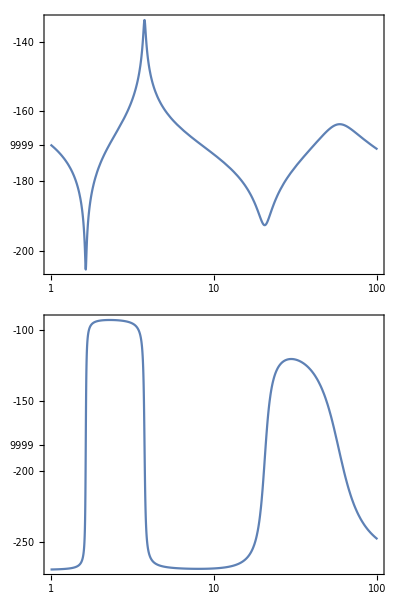

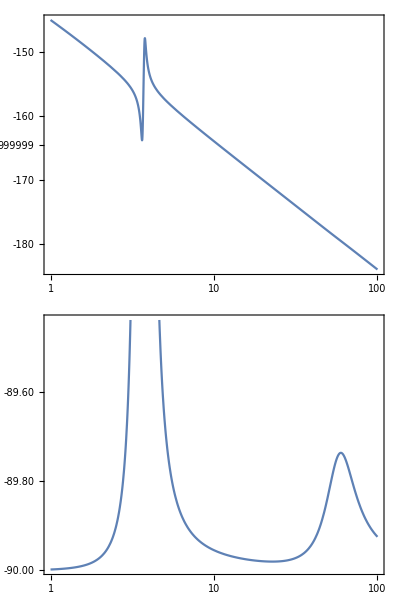

```mathematica
BodePlot[fq2y];
BodePlot[fDttF, {1, 10^2}]
BodePlot[fDttT, {1, 10^2}]
```

### Decomposição em frações parciais

```mathematica
FP = Apart[TF[s]]; 
FP//MatrixForm;
```

### Teste de controlabilidade do sistema

```mathematica
SSc = StateSpaceModel[{𝔸/.(rep)/.(Subscript[Φ, 0]->18*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹/.(rep)/.(Subscript[Φ, 0]->13*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂ, 𝔻c}] ;
CM = ControllabilityMatrix[SSc];
CM//MatrixForm
```

(0 | 0 | -0.00025 | 0. | 0.00730259 | -5.50027×10^-6 | 0.62513 | -0.000457585 | -42.5564 | 0.0318079 | -847.015 | 0.60951
0 | 0 | 0.0000120978 | -2.15283×10^-7 | -0.000323057 | 2.65355×10^-7 | -0.0269123 | 0.0000227085 | 1.86017 | -0.00139078 | 35.588 | -0.0256206
0 | 0 | -2.15283×10^-7 | 6.31275×10^-8 | 5.61132×10^-6 | -4.60906×10^-9 | 0.000467441 | -3.91421×10^-7 | -0.0323098 | 0.0000241569 | -0.618122 | 0.000444997
-1/4000 | 0 | 0.00730259 | -5.50027×10^-6 | 0.62513 | -0.000457585 | -42.5564 | 0.0318079 | -847.015 | 0.60951 | 166624. | -123.856
0.0000120978 | -2.15283×10^-7 | -0.000323057 | 2.65355×10^-7 | -0.0269123 | 0.0000227085 | 1.86017 | -0.00139078 | 35.588 | -0.0256206 | -7241.44 | 5.38226
-2.15283×10^-7 | 6.31275×10^-8 | 5.61132×10^-6 | -4.60906×10^-9 | 0.000467441 | -3.91421×10^-7 | -0.0323098 | 0.0000241569 | -0.618122 | 0.000444997 | 125.778 | -0.0934857)

```mathematica
Rk = MatrixRank[CM]
```

6

## Pós toque

### Modelo incluindo trem de pouso frontal

-Graphics-

```mathematica
Subscript[𝕢, T][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t]};
Subscript[𝕧, T][t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = {Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, Subscript[𝕧, T][t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, PO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor P-O*);
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, GO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor G-O*);
Subscript[ρ, FO] = {Subscript[D, FO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, FO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor F-O*);
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[F, f] = {0, -Subscript[k, Tf]*(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]), t]), 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, Tf] = Cross[Subscript[ρ, FO], Subscript[F, f]] //FullSimplify;
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso] - Subscript[M, Tf])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m e mf) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[Subscript[𝕧, T][t][[1]], t]) + Subscript[k, r]*(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]) - Subscript[c, t]*(D[(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]), t]) //FullSimplify;
Subscript[TMB, mf] = Subscript[m, f]*(D[Subscript[𝕧, T][t][[4]], t]) + Subscript[k, rf]*(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]) + Subscript[c, rf]*(D[(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]), t]) - Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) + Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) - Subscript[L, ext][[2]] //FullSimplify;
noequi =  Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) //FullSimplify;
```

### O espaço de estados

```mathematica
DINf = {Subscript[TMB, m], Subscript[TMB, M], TQMA, Subscript[TMB, mf]};

Solf[t_] = Flatten @ Solve[
	(# == 0)& /@ DINf,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
𝕩f[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Ff = (𝕩f'[t] /.Solf[t]); 
Ff //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-4 g M Cos[Φ_0+θ[t]]^2+Sin[2 (Φ_0+θ[t])] (2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol)+M D_GO (S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2-4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2-4 Cos[Φ_0+θ[t]]^2 D_FO^2 (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+4 Cos[Φ_0+θ[t]]^2 D_FO (k_Tf (-q_2[t]+q_3[t])+c_Tf (-q_2'[t]+q_3'[t])))+2 J_oz (-S ρ C_L (u_longit+u_vento)^2+2 D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])-2 (k_t (q_1[t]-q_2[t])+k_Tf (-q_2[t]+q_3[t])+c_t (q_1'[t]-q_2'[t])+c_Tf (-q_2'[t]+q_3'[t]))))/(4 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(-S ρ Sec[Φ_0+θ[t]] C_L D_PO (u_longit+u_vento)^2+2 D_FO^2 k_Tf Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit^2 Tan[Φ_0+θ[t]]-2 S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit u_vento Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_vento^2 Tan[Φ_0+θ[t]]+2 Sec[Φ_0+θ[t]] D_FO k_Tf q_2[t]-2 Sec[Φ_0+θ[t]] D_FO k_Tf q_3[t]+2 c_Tf D_FO^2 θ'[t]+2 M D_GO^2 Tan[Φ_0+θ[t]] θ'[t]^2+2 Sec[Φ_0+θ[t]] c_Tf D_FO q_2'[t]+D_GO (S ρ Sec[Φ_0+θ[t]] C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])-2 (D_FO (k_Tf Tan[Φ_0+θ[t]]+c_Tf θ'[t])+Sec[Φ_0+θ[t]] (-g M+g M μ_rol Tan[Φ_0+θ[t]]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))-2 Sec[Φ_0+θ[t]] c_Tf D_FO q_3'[t])/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0

```mathematica
POSequif = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> - Subscript[Φ, 0], Subscript[q, 3][t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINflin = Linearize[DINf, POSequif]; (*ELS -> Equação dinâmica não-linear*)

Solflin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINflin,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
Subscript[𝕩f, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Subscript[Ff, lin] = (Subscript[𝕩f, lin]'[t] /.Solflin[t]);
Subscript[Ff, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-2 g M+(2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol θ[t])+M D_GO (S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ[t])-2 D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])))-J_oz (S ρ C_L (u_longit+u_vento)^2-2 (k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))/(2 M (M D_GO^2-J_oz))
(-S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ[t])+D_GO (S ρ C_L (u_longit+u_vento)^2 (1+μ_rol θ[t])-2 (-g M+g M μ_rol θ[t]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t])))+2 D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])))/(2 M D_GO^2-2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

```mathematica
𝔸f = CoefficientArrays[Subscript[Ff, lin], Subscript[𝕩f, lin][t]][[2]]//Normal; 
𝔸f //FullSimplify//MatrixForm;

𝔹f = CoefficientArrays[Subscript[Ff, lin], 𝕦[t]][[2]]//Normal; 
𝔹f //MatrixForm;

ℂf = { {0,1,0,0,0,0,0,0}, {0,0,1,0,0,0,0,0}, {0,0,0,0,0,1,0,0}, {0,0,0,0,0,0,1,0}};
ℂf //MatrixForm;

𝔻f = {{0,0},{0,0},{0,0},{0,0}};
𝔻f //MatrixForm;
 
𝕩f[t] //MatrixForm ;
𝕩f'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
```

### Substituindo os valores numéricos

```mathematica
rep2 = {Subscript[D, FO]->18.2, Subscript[k, Tf]->11486800/2, Subscript[c, Tf]-> 1021960/2, Subscript[k, rf]-> 13600000/4, Subscript[c, rf]-> 9700/4, Subscript[m, f]->1000};
SS = StateSpaceModel[{𝔸f/.(rep2)/.(rep)/.(Subscript[u, longit]->280/3.6)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹f/.(rep2)/.(rep)/.(Subscript[u, longit]->280/3.6)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂf, 𝔻f}]
```

0000100000000001000000000010000000000100-32117/1028717/1000-13987/50025549/10000034097/40139.445-185.993-847.37346.54741.24062-5.38186-75.37064.1412400-2.54673-2.80141-97.27635.34814-0.0226578-0.453157-8.659820.47581500028717/5104530.-45717/5025549/509299.84-102681/200340097/400100000000001000000000000100000000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2481FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TFf = TransferFunctionModel[SS, s]
```

(1.81175×10^10+1.78685×10^9 s+9.62739×10^8 s^2+7.83792×10^7 s^3+820346. s^4+14502. s^5)/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)(13.051 (9.9222×10^6+978561. s+276158. s^2+18415.1 s^3+176.748 s^4+s^5))/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)(0.000087738+6.41367×10^6 s+5.37558×10^7 s^2+5.45338×10^6 s^3+60711.6 s^4+1610.07 s^5)/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)(-6.41367×10^6-627674. s-19891.4 s^2+395.534 s^3+10.8621 s^4+1.09891 s^5)/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)(1.81175×10^10 s+1.78685×10^9 s^2+9.62739×10^8 s^3+7.83792×10^7 s^4+820346. s^5+14502. s^6)/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)(1.29495×10^8 s+1.27712×10^7 s^2+3.60414×10^6 s^3+240335. s^4+2306.74 s^5+13.051 s^6)/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)(6.41367×10^6 s^2+5.37558×10^7 s^3+5.45338×10^6 s^4+60711.6 s^5+1610.07 s^6)/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)(1.09891 (-5.83642×10^6 s-571181. s^2-18101.1 s^3+359.935 s^4+9.88443 s^5+s^6))/(1.81175×10^10+1.91634×10^9 s+2.09004×10^9 s^2+1.91715×10^8 s^3+3.34524×10^7 s^4+2.08137×10^6 s^5+28041.9 s^6+555.421 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s241.8117545806678547e1013.0510119067039360.000087738037109375-6.4136682643470755e61.8117545806678566e101.2949479107572792e86.413668264442444e61.09890503955102761.8117545806678474e101.8117545806678474e101.8117545806678474e101.8117545806678474e101.8117545806678474e101.8117545806678474e101.8117545806678474e101.8117545806678474e101FalseFalseFalseAutomaticNoneAutomatic

```mathematica
(1.745282603075172*^11+3.118329179482092*^10 s+6.747824583214443*^9 s^2+7.611950276458383*^8 s^3+2.597126294092075*^7 s^4+56530.10003328137 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(1.2447971507229614*^8+2.224102429483795*^7 s+4.812786651264191*^6 s^2+542911.1594238281 s^3+18523.621362268925 s^4+40.31926252413541 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.0001220703125+7.141307544117928*^7 s^2+8.572115094852805*^6 s^3+211166.63687618077 s^4+1225.9669270208105 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.000030517578125+50934.32586860657 s^2+6113.935030817985 s^3+150.61149835586548 s^4+0.8744028815999627 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(56530.10003328111 (3.0873509900878775*^6 s+551622.7952270083 s^2+119366.93158585922 s^3+13465.304805717626 s^4+459.42361548326704 s^5+s^6))/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(40.319262523757054 (3.087350990086266*^6 s+551622.7952267507 s^2+119366.93158580044 s^3+13465.304805710715 s^4+459.4236154830451 s^5+s^6))/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.000034332275390625 s-1.9073486328125*^-6 s^2+7.141307544117641*^7 s^3+8.572115094852641*^6 s^4+211166.6368761873 s^5+1225.9669270210143 s^6)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.000034332275390625 s-1.9073486328125*^-6 s^2+50934.325866103165 s^3+6113.93503087759 s^4+150.6114983614534 s^5+0.8744028817745857 s^6)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s241.745282603075172e111.2447971507229614e8-0.0001220703125-0.00003051757812556530.1000332811140.319262523757054-0.000034332275390625-0.0000343322753906251.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111FalseFalseFalseAutomaticNoneAutomatic
```

(1.74528×10^11+3.11833×10^10 s+6.74782×10^9 s^2+7.61195×10^8 s^3+2.59713×10^7 s^4+56530.1 s^5)/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)(1.2448×10^8+2.2241×10^7 s+4.81279×10^6 s^2+542911. s^3+18523.6 s^4+40.3193 s^5)/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)(-0.00012207+7.14131×10^7 s^2+8.57212×10^6 s^3+211167. s^4+1225.97 s^5)/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)(-0.0000305176+50934.3 s^2+6113.94 s^3+150.611 s^4+0.874403 s^5)/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)(56530.1 (3.08735×10^6 s+551623. s^2+119367. s^3+13465.3 s^4+459.424 s^5+s^6))/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)(40.3193 (3.08735×10^6 s+551623. s^2+119367. s^3+13465.3 s^4+459.424 s^5+s^6))/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)(-0.0000343323 s-1.90735×10^-6 s^2+7.14131×10^7 s^3+8.57212×10^6 s^4+211167. s^5+1225.97 s^6)/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)(-0.0000343323 s-1.90735×10^-6 s^2+50934.3 s^3+6113.94 s^4+150.611 s^5+0.874403 s^6)/(1.74528×10^11+3.13078×10^10 s+8.98982×10^9 s^2+1.05886×10^9 s^3+9.49636×10^7 s^4+5.99676×10^6 s^5+157967. s^6+796.998 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s241.745282603075172e111.2447971507229614e8-0.0001220703125-0.00003051757812556530.1000332811140.319262523757054-0.000034332275390625-0.0000343322753906251.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[TFf] //MatrixForm
```

((-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ) | (-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ)
(-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ) | (-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ)
(-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ) | (-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ)
(-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ) | (-508.036
-16.6109
-14.5526-55.9032 ⅈ
-14.5526+55.9032 ⅈ
-0.785799-7.79473 ⅈ
-0.785799+7.79473 ⅈ
-0.0486112-3.23732 ⅈ
-0.0486112+3.23732 ⅈ))

```mathematica
TransferFunctionZeros[TFf] //MatrixForm
```

({-21.4971-65.8457 ⅈ,-21.4971+65.8457 ⅈ,-13.2908,-0.1413-4.42403 ⅈ,-0.1413+4.42403 ⅈ} | {-79.8501-96.231 ⅈ,-79.8501+96.231 ⅈ,-16.0183,-0.514623-6.27292 ⅈ,-0.514623+6.27292 ⅈ}
{-13.4666-53.9836 ⅈ,-13.4666+53.9836 ⅈ,-10.6535,-0.120789,-1.36799×10^-11} | {-12.3162-7.73984 ⅈ,-12.3162+7.73984 ⅈ,-7.29839-29.7774 ⅈ,-7.29839+29.7774 ⅈ,29.3448}
{-21.4971-65.8457 ⅈ,-21.4971+65.8457 ⅈ,-13.2908,-0.1413-4.42403 ⅈ,-0.1413+4.42403 ⅈ,0} | {-79.8501-96.231 ⅈ,-79.8501+96.231 ⅈ,-16.0183,-0.514623-6.27292 ⅈ,-0.514623+6.27292 ⅈ,0}
{-13.4666-53.9836 ⅈ,-13.4666+53.9836 ⅈ,-10.6535,-0.120789,0,0} | {-12.3162-7.73984 ⅈ,-12.3162+7.73984 ⅈ,-7.29839-29.7774 ⅈ,-7.29839+29.7774 ⅈ,0,29.3448})

## Exportando o aquivo .m do espaço de estados

Para exportar outro espaço de estados, basta substituir o argumento da 4 linha da terceira célula de código por:
WriteString[fileD, (#/.(({ii_}→vv_):>(StringReplace[StringReplace[ToString @ StringForm[“    ``;”, (vv /. crule //CForm)], csqrule], csorule]<>”\n”)))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩’[t]/.NOMEDASOLUCAO[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));

```mathematica
(*Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];*)
```

```mathematica
(*crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};*)
```

```mathematica
(*fileD = OpenWrite["trab_esp_linearizado0.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(Subscript[𝕩f, lin]'[t]/.Solflin[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));
WriteString[fileD, "\n"];
Close[fileD];*)
```